```mathematica
(* Shooting Method for Solving Differential eq.s*)
(*1:- Can be used to Solve Boundary value Problems.
2:- By Shooting Method B.V problem becomes iniatial Value Problem.  *)
```

```mathematica
(* Using Shooting Method 
=>From Shooting point we shoot the values of dep. variable at varying shooting Angles.
(*Special Remarks about Shooting Method : in mathematica Shooting method can be implemented by Using NDSolve[] Commandand due to its pure function Solutions property. 
(* Points for converting a B.V problem into an iniatial value Problem.
1:- List out the B.C or  boundary points.
2:- decide shooting and target point out of the boundary points.
3:- determine the shooting angle or shooting slope at the shooting point such that u sucessfully hit the target. *)
```

```mathematica
Note: (* Tan[Shooting angle]= Shooting Slope= Gradient  ,,,,, e.g  y'[shooting point].
4:- Thus the B.V problem will also become an initial value problem.*)
Example:- solve the differential eq. : x''[t]+ω^2 x[t]==0, by using Shooting method.The B.c are ;x[0]=2;x[T]=2;
(* Solution *)
```

```mathematica
(*we decided that, t=0 is shooting point and t=T is a Target point. Here Shooting Angle can be found by NDSolve[].*)
```

```mathematica
(*Def. Trajectory as a function of unknown parameter ,i.e the shooting slope.*)
ω=20;T=2Pi/ω;deq= x''[t]+ω^2 x[t]==0;
xend[m_]:=x[T]/.NDSolve[{deq,x[0]==2,x'[0]==m},x,{t,0,T}][[1]];(*initial conditions.*)
Plot[xend[m],{m,-0.1,0.1}];
Do[if[Abs[xend[m]-2]<0.00001,slope=m,Print["m=",m]],{m,-0.1,0.1,0.001}];(*Abs[xend[m]-2]<0.00001? . Ans: it may not hit the target,that's why we use threashold value.  *)
```

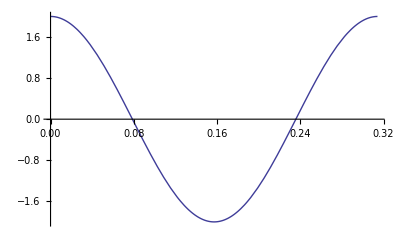

```mathematica
shootSol=x[t]/.NDSolve[{deq,x[0]==2,x'[0]==slope},x,{t,0,T}][[1]];
Plot[shootSol,{t,0,T}]
```